```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data$par=Import["test-par.out","CSV"];
data$opt=Import["test-opt.out","CSV"];
data$ref=Import["test-ref.out","CSV"];
data$f90=Import["test-f90.out","CSV"];
data$f91=Import["test-f91.out","CSV"];
data$f92=Import["test-f92.out","CSV"];
```

```mathematica
plot$list={
data$par,data$opt,
data$ref,data$f90,data$f91,data$f92
};
plot$colors={
Black,Red,
Gray,Darker@Cyan,Darker@Green,Blue
};
```

```mathematica
plotResult[opts___]:=Show[
ListPlot[
Evaluate[#⟦2;;⟧&/@plot$list],
opts,
PlotLabel->Style["shwater2d in C++, C and f90 on Beskow; problem size 2000×2000" ,Black,16],
ImageSize->1000,Joined->True,
PlotStyle->plot$colors,
PlotMarkers->Automatic,
PlotLegends->Evaluate[Placed[Style[#⟦1,1,1⟧,#⟦2⟧,14]&/@Transpose[{plot$list,plot$colors}],Scaled[{0.8,0.7}]]],
ClippingStyle->None,
PlotTheme->"Scientific",FrameLabel->{"number of cores","elapsed time"},BaseStyle->{Directive[16]}
],
Plot[
{
data$opt⟦2,2⟧*data$opt⟦2,1⟧/n
},
{n,0.1,64},
PlotRange->Full,
PlotStyle->{{Lighter@Red,Dashed}},
PlotLegends->Placed[{Style["C++ theoretical",Lighter@Red,14]},Scaled[{0.8,0.7}]],
PlotTheme->"Scientific",BaseStyle->{Directive[16]}
]
]
```

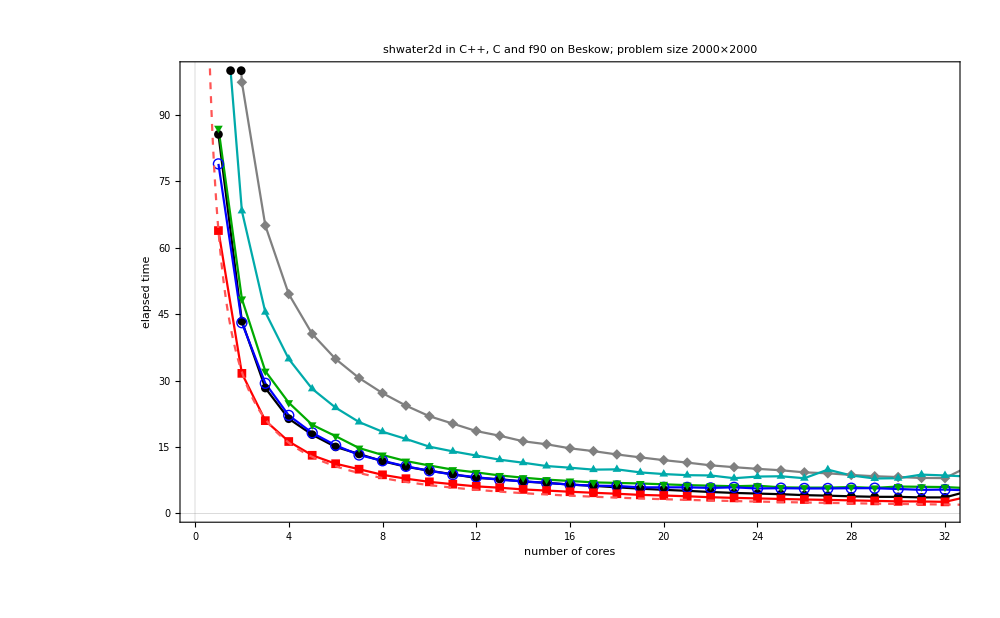

```mathematica
plotResult[PlotRange->{{0,32},{0,100}}]
Export["plot1.pdf",%];
```

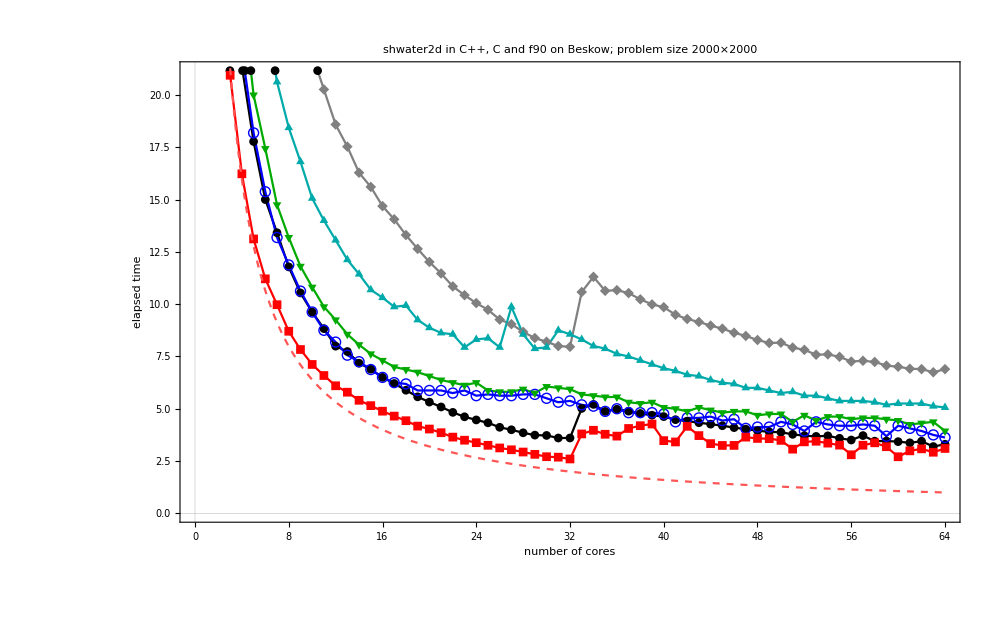

```mathematica
plotResult[]
Export["plot2.pdf",%];
```

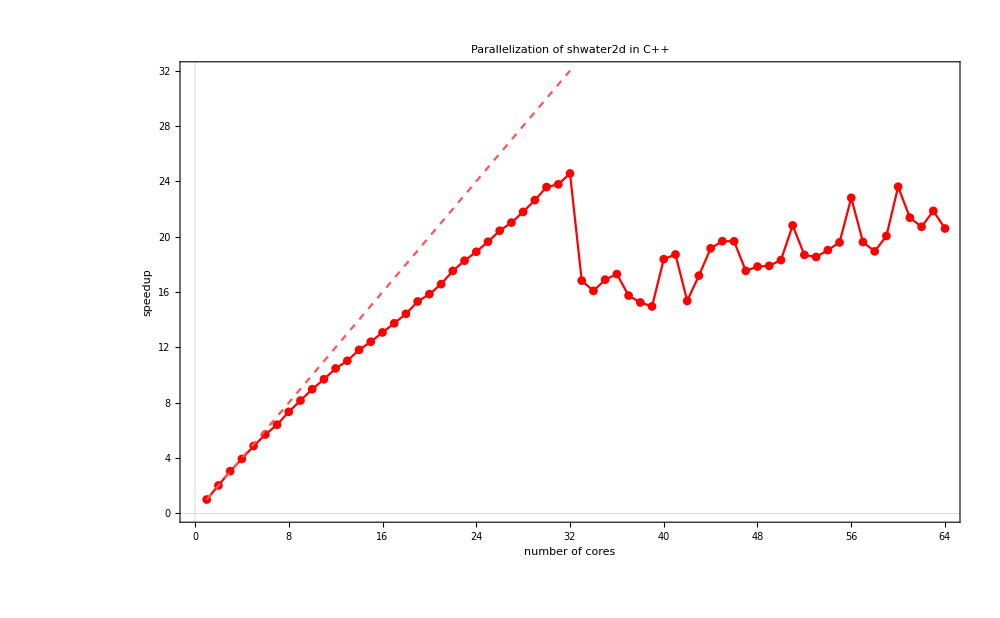

```mathematica
Show[ListPlot[
Table[
{n,(data$opt⟦2,2⟧*data$opt⟦2,1⟧)/data$opt⟦n+1,2⟧},
{n,64}
],
PlotRange->{0,32},
PlotLabel->Style["Parallelization of shwater2d in C++" ,Black,16],
ImageSize->1000,Joined->True,
PlotStyle->plot$colors⟦2⟧,
PlotMarkers->Automatic,ClippingStyle->None,
PlotTheme->"Scientific",FrameLabel->{"number of cores","speedup"},BaseStyle->{Directive[16]}
],
Plot[n,{n,1,32},PlotStyle->{Lighter@Red,Dashed}]
]
Export["plot3.pdf",%];
```

```mathematica
data$opt2=Import["test-opt2.out","CSV"];
data$opt3=Import["test-opt3.out","CSV"];
data$opt4=Import["test-opt4.out","CSV"];
```

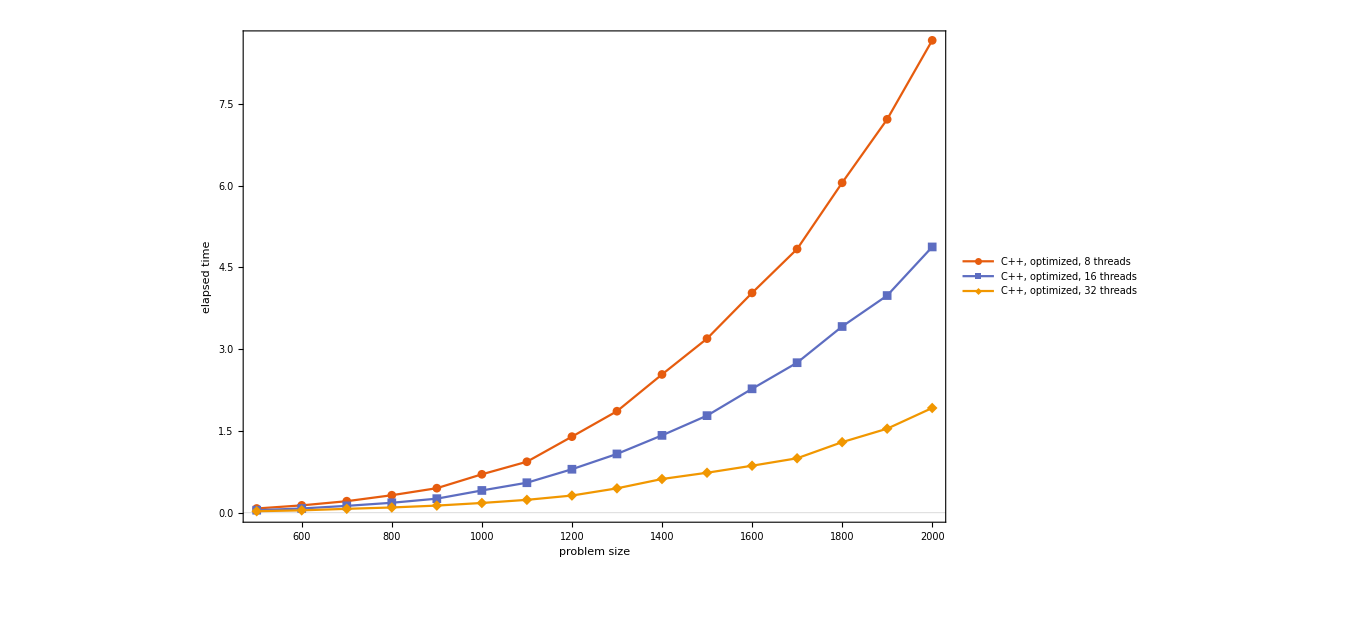

```mathematica
ListPlot[
{
data$opt2⟦2;;,{1,-1}⟧,
data$opt3⟦2;;,{1,-1}⟧,
data$opt4⟦2;;,{1,-1}⟧
},
PlotLegends->Placed[
{
Style[StringRiffle[data$opt2⟦1⟧,", "],Black,14],
Style[StringRiffle[data$opt3⟦1⟧,", "],Black,14],
Style[StringRiffle[data$opt4⟦1⟧,", "],Black,14]
},{0.2,0.5}],
ImageSize->1000,Joined->True,
PlotMarkers->Automatic,ClippingStyle->None,
PlotTheme->"Scientific",FrameLabel->{"problem size","elapsed time"},BaseStyle->{Directive[16]}
]
Export["plot4.pdf",%];
```

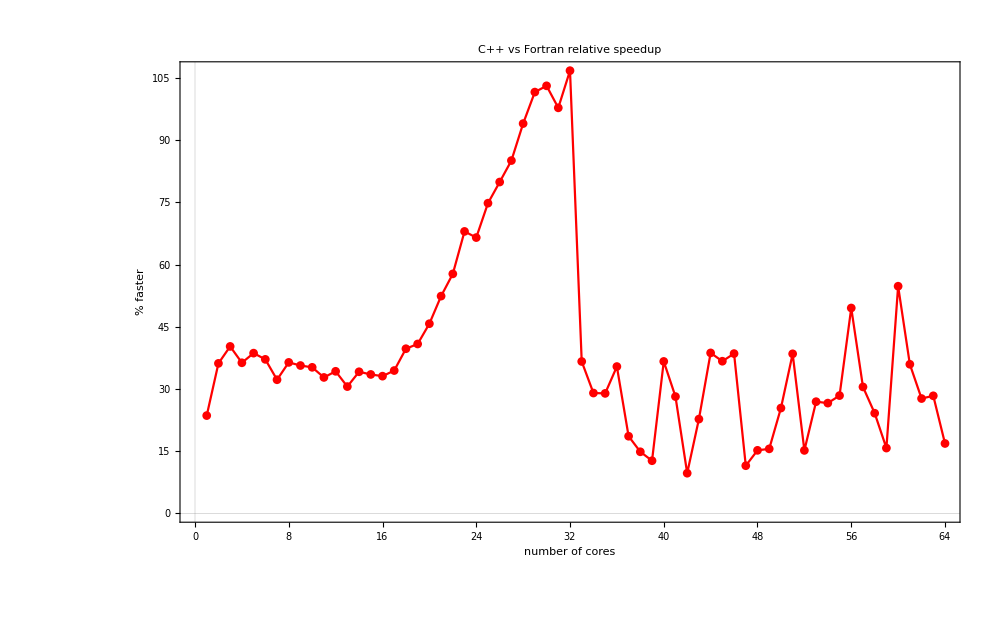

```mathematica
ListPlot[
Transpose@{data$f92⟦2;;,-2⟧,100#-100&/@(data$f92⟦2;;,-1⟧/data$opt⟦2;;,-1⟧)},
PlotLabel->Style["C++ vs Fortran relative speedup" ,Black,16],
ImageSize->1000,Joined->True,
PlotStyle->plot$colors⟦2⟧,
PlotMarkers->Automatic,ClippingStyle->None,
PlotTheme->"Scientific",FrameLabel->{"number of cores","% faster"},BaseStyle->{Directive[16]}
]
Export["plot5.pdf",%];
```